## Что-то...

#### Симметричный

```mathematica
ClearAll["Global`*"]
NotebookDirectory[];
n = 2;
plots=ReadList[Evaluate[StringJoin[NotebookDirectory[],"Integtgro_interpolation_mult.txt"]],Table[Real,n+1]];
k = plots⟦Length[plots]⟧⟦1⟧+1;
m = plots⟦Length[plots]⟧⟦2⟧+1;
TAll = {};
For[j=0,j<k,j++;
T = {};
For[i = 0,i <m,i++;
T = AppendTo[T,{plots⟦(j-1)*m +i⟧⟦2⟧,plots⟦(j-1)*m+i⟧⟦3⟧}]];
TAll = AppendTo[TAll,T]]
```

```mathematica
Manipulate[ListContourPlot[TAll⟦i⟧],{i,1,k-1}]
```

```mathematica
TAll⟦1⟧
```

{{0.,0.04},{1.,6.98947},{2.,3.66237},{3.,1.44451},{4.,-0.378081},{5.,-0.361362},{6.,-0.246409},{7.,-0.0503216},{8.,-0.0148767},{9.,-0.00732916},{10.,-0.0090472},{11.,-0.122043},{12.,-0.102305},{13.,-0.0172909},{14.,0.0185859},{15.,0.0191116}}

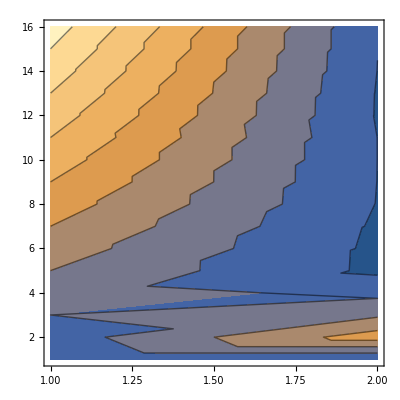

```mathematica
ListContourPlot[TAll⟦1⟧]
```